Vaje z dne 19. 4.

### 1. naloga

Želimo vsakemu profesorju prirediti predmet tako, da bo skupno ovrednotenje vseh profesorjev čim večje. V tabeli imamo profesorje zapisane po vrsticah in predmete po stolpcih. Elementi matrike povedo, kako je profesor ovrednoten pri posameznem predmetu.

```mathematica
profesorji=({{80, 75, 90, 85}, {95, 90, 90, 97}, {85, 95, 88, 91}, {93, 91, 80, 84}, {91, 92, 93, 88}});
```

```mathematica
{m,n}=Dimensions[profesorji];
```

```mathematica
X=Table[Subscript[x, i,j],{i,m},{j,n}];
kriterijskaUcitelji=Plus@@Flatten[profesorji*X];
```

Dodamo pogoje. Vsak učitelj uči največ 1 predmet. En učitelj ostene brez predmeta. Zato je vsota po vrsticah ≤ 1. Vsak predmet dobi učitelja. Zato je vsota po stolpcih == 1.

```mathematica
pogojUcitelji=Plus@@#≤1&/@X;
pogojPredmeti=Plus@@#==1&/@Transpose[X];
pogojNenegativnost=#≥0&/@Flatten[X];
```

```mathematica
resitevUcitelji=Maximize[Join[
{kriterijskaUcitelji,
pogojUcitelji,
pogojPredmeti,
pogojNenegativnost}
],
Flatten[X],
Integers
]
```

{378,{x_(1,1)→0,x_(1,2)→0,x_(1,3)→0,x_(1,4)→0,x_(2,1)→0,x_(2,2)→0,x_(2,3)→0,x_(2,4)→1,x_(3,1)→0,x_(3,2)→1,x_(3,3)→0,x_(3,4)→0,x_(4,1)→1,x_(4,2)→0,x_(4,3)→0,x_(4,4)→0,x_(5,1)→0,x_(5,2)→0,x_(5,3)→1,x_(5,4)→0}}

```mathematica
X/.resitevUcitelji⟦2⟧//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0)

### 2. naloga

#### a)

Razporedi učence po šolah tako, da bo skupni čas potovanja do šole najmanjši. V vsaki šoli je lahko največ 400 učencev. Vrstice so različni predeli mesta: sever, jug, vzhod, zahod, center. Stolpci so različe šole: Addison, Beeks, Canfield, Daley. Elementi so čas, ki ga učenci iz posameznega področja rabijo, da pridejo v določeno šolo.

```mathematica
casPotovanja=({{12, 23, 35, 17}, {26, 15, 21, 27}, {18, 20, 22, 31}, {29, 24, 35, 10}, {15, 10, 23, 16}});
```

```mathematica
{k,l}=Dimensions[casPotovanja];
```

```mathematica
XSola=Table[Subscript[x, i,j],{i,k},{j,l}];
kriterijskaSola=Plus@@Flatten[casPotovanja*X];
```

Dodamo pogoje na vrstice. Pogoji so navedeni v nalogi, npr. v severnem območju (prva vrstica) živi 250 otrok, v južnem (druga vrstica) 340 otrok, itd. Pogoj na stolpce je, da je lahko v vsaki šoli največ 400 otrok.

```mathematica
populacija={250,340,310,210,290};
```

```mathematica
pogojPodrocja=Table[Plus@@XSola⟦i⟧==populacija⟦i⟧,{i,k}];
pogojSole=Plus@@#≤400&/@Transpose[XSola];
pogojNenegativnost=#≥0&/@Flatten[XSola];
```

```mathematica
resitevSole=Minimize[Join[
{kriterijskaSola,
pogojPodrocja,
pogojSole,
pogojNenegativnost}
],
Flatten[XSola],
Integers
]
```

{20700,{x_(1,1)→250,x_(1,2)→0,x_(1,3)→0,x_(1,4)→0,x_(2,1)→0,x_(2,2)→255,x_(2,3)→85,x_(2,4)→0,x_(3,1)→150,x_(3,2)→0,x_(3,3)→160,x_(3,4)→0,x_(4,1)→0,x_(4,2)→0,x_(4,3)→0,x_(4,4)→210,x_(5,1)→0,x_(5,2)→145,x_(5,3)→0,x_(5,4)→145}}

#### b)

Sedaj želimo najti rešitev za primer, ko je v vsaki šoli enako število učencev. Vseh učencev je 1400, šole so 4, zato jih mora biti v vaki šoli 1400/4 = 350. Spremenimo torej pogoj na šole. Vse drugo ostane enako.

```mathematica
pogojSoleEnakomerno=Plus@@#==350&/@Transpose[XSola]
```

{x_(1,1)+x_(2,1)+x_(3,1)+x_(4,1)+x_(5,1)==350,x_(1,2)+x_(2,2)+x_(3,2)+x_(4,2)+x_(5,2)==350,x_(1,3)+x_(2,3)+x_(3,3)+x_(4,3)+x_(5,3)==350,x_(1,4)+x_(2,4)+x_(3,4)+x_(4,4)+x_(5,4)==350}

```mathematica
resitevSoleEnak = Minimize[Join[
{kriterijskaSola,
pogojPodrocja,
pogojSoleEnakomerno,
pogojNenegativnost}
],
Flatten[XSola],
Integers
]
```

{21200,{x_(1,1)→250,x_(1,2)→0,x_(1,3)→0,x_(1,4)→0,x_(2,1)→0,x_(2,2)→200,x_(2,3)→140,x_(2,4)→0,x_(3,1)→100,x_(3,2)→0,x_(3,3)→210,x_(3,4)→0,x_(4,1)→0,x_(4,2)→0,x_(4,3)→0,x_(4,4)→210,x_(5,1)→0,x_(5,2)→150,x_(5,3)→0,x_(5,4)→140}}

### 3. naloga

Poišči najkrajšo pot med vsakima dvema vozliščema v grafu. Najprej iz slike grafa 3. naloge izpišemo matriko sosednosti.

```mathematica
matrikaSosednosti=({{0, 15, 13, 5, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 12, 0}, {0, 2, 0, 18, 0, 6, 0, 0, 0}, {0, 0, 0, 0, 4, 0, 0, 0, 99}, {0, 0, 3, 0, 0, 1, 9, 0, 14}, {0, 8, 0, 0, 0, 0, 0, 17, 0}, {0, 0, 0, 0, 0, 16, 0, 7, 10}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 11, 0}});
```

Zamenjajmo vse ničle v neskončnosti.

```mathematica
matrikaSosednosti = matrikaSosednosti/.{0->∞};
```

Sedaj naredimo graf iz matrike.

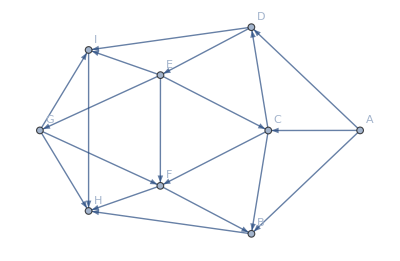

```mathematica
graf=WeightedAdjacencyGraph[matrikaSosednosti, VertexLabels->{1->"A", 2->"B",3->"C",4->"D",5->"E",6->"F",7->"G",8->"H",9->"I"}]
```

Spodnji ukaz nam vrne vozlišča, preko katerih pridemo po najkrajši poti od prvega podanega vozlišča do drugega.

```mathematica
FindShortestPath[graf,1,7]
```

{1,4,5,7}

Poiščimo sedaj najkrajše poti v celotnem grafu. Namesto zank v Mathematici uporabljamo vgrajene funkcije, npr. Table ali Range.

```mathematica
(Table[FindShortestPath[graf, i, j],{i,9}, {j,9}])//MatrixForm
```

({1} | {1,4,5,3,2} | {1,4,5,3} | {1,4} | {1,4,5} | {1,4,5,6} | {1,4,5,7} | {1,4,5,7,8} | {1,4,5,9}
{} | {2} | {} | {} | {} | {} | {} | {2,8} | {}
{} | {3,2} | {3} | {3,4} | {3,4,5} | {3,6} | {3,4,5,7} | {3,2,8} | {3,4,5,9}
{} | {4,5,3,2} | {4,5,3} | {4} | {4,5} | {4,5,6} | {4,5,7} | {4,5,7,8} | {4,5,9}
{} | {5,3,2} | {5,3} | {5,3,4} | {5} | {5,6} | {5,7} | {5,7,8} | {5,9}
{} | {6,2} | {} | {} | {} | {6} | {} | {6,8} | {}
{} | {7,6,2} | {} | {} | {} | {7,6} | {7} | {7,8} | {7,9}
{} | {} | {} | {} | {} | {} | {} | {8} | {}
{} | {} | {} | {} | {} | {} | {} | {9,8} | {9})

Še bolj optimalno si je definirati funkcijo FindShortestPathFunction na danem grafu in jo nato uporabiti na vsakem vozlišču.

```mathematica
najkrajsePoti = FindShortestPath[graf];
(matrikaNajkrajsihPoti =Table[najkrajsePoti[i,j],{i,9},{j,9}])//MatrixForm
```

({1} | {1,4,5,3,2} | {1,4,5,3} | {1,4} | {1,4,5} | {1,4,5,6} | {1,4,5,7} | {1,4,5,7,8} | {1,4,5,9}
{} | {2} | {} | {} | {} | {} | {} | {2,8} | {}
{} | {3,2} | {3} | {3,4} | {3,4,5} | {3,6} | {3,4,5,7} | {3,2,8} | {3,4,5,9}
{} | {4,5,3,2} | {4,5,3} | {4} | {4,5} | {4,5,6} | {4,5,7} | {4,5,7,8} | {4,5,9}
{} | {5,3,2} | {5,3} | {5,3,4} | {5} | {5,6} | {5,7} | {5,7,8} | {5,9}
{} | {6,2} | {} | {} | {} | {6} | {} | {6,8} | {}
{} | {7,6,2} | {} | {} | {} | {7,6} | {7} | {7,8} | {7,9}
{} | {} | {} | {} | {} | {} | {} | {8} | {}
{} | {} | {} | {} | {} | {} | {} | {9,8} | {9})

Kako bi sedaj dobili še dolžine poti? Naredimo funkcijo, ki nam jo izračuna. Uporabimo kombinacije ESC + Sum / _ / 5 / [[ / ]] + ESC. Funkcija v matriki sosednosti  poišče razdalje med dvema sosednjima vozliščema.

```mathematica
dolzina[pot_]:=
If[Length[pot]==0,∞,
∑_(i=1)^(Length[pot]-1) matrikaSosednosti⟦pot⟦i⟧,pot⟦i+1⟧⟧];
```

Na spodnjem primeru vidimo, da je najkrajša dolžina od vozlišča 1 do vozlišča 8 preko vozlišča 2 enaka 27. Če pogledamo v matriko sosednosti, vidimo, da je cena razdalje od vozlišča 1 do vozlišča 2 enaka 15 in od vozlšča 2 do vozlišča 8 enaka 12.

```mathematica
dolzina[{1,2,8}]
```

27

Razdalja od 4 do 5 + razdalja od 5 do 3 + razdalja od 3 do 2.

```mathematica
dolzina[{4,5,3,2}]
```

9

```mathematica
dolzina[{1}]
```

0

Sedaj lahko izračunamo razdalje v matriki najkrajših poti. Tak rezultat bi nam vrnil tudi Floyd-Warshallow algoritem.

```mathematica
Table[dolzina[matrikaNajkrajsihPoti⟦i,j⟧],{i,9},{j,9}]//MatrixForm
```

(0 | 14 | 12 | 5 | 9 | 10 | 18 | 25 | 23
∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | 12 | ∞
∞ | 2 | 0 | 18 | 22 | 6 | 31 | 14 | 36
∞ | 9 | 7 | 0 | 4 | 5 | 13 | 20 | 18
∞ | 5 | 3 | 21 | 0 | 1 | 9 | 16 | 14
∞ | 8 | ∞ | ∞ | ∞ | 0 | ∞ | 17 | ∞
∞ | 24 | ∞ | ∞ | ∞ | 16 | 0 | 7 | 10
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 11 | 0)

Kako bi aplicirami funkcijo za dolžino poti na matriki najkrajših poti? 
f/@seznam pomeni, da funkcijo f uporabimo na vsakem elementu seznama. Če uporabimo f/@matrika pomeni, da bomo funkcijo f uporabili na vseh vrsticah matrike. Mi pa želimo uporabiti funkcijo f na vseh elementih vsake vrstice v matriki.

```mathematica
f/@{1,4,5,3,2}
```

{f[1],f[4],f[5],f[3],f[2]}

Drug način zapisa za f/@seznam je Funciton[x,f/@seznam]. Gre za diskretno podano funkcijo, torej funkcijo, ki ji ni treba podati imena. V našem primeru je to predpis, ki slika f na vsak element seznama.

```mathematica
Function[x,f/@x][{1,4,5,3,2}]
```

{f[1],f[4],f[5],f[3],f[2]}

Spodnji ukaz uporabi funkcijo f na vsakem elementu matrike.

```mathematica
f/@#&/@matrikaNajkrajsihPoti;
```

```mathematica
dolzina/@#&/@matrikaNajkrajsihPoti //MatrixForm
Map[dolzina,matrikaNajkrajsihPoti,{2}]//MatrixForm;
```

(0 | 14 | 12 | 5 | 9 | 10 | 18 | 25 | 23
∞ | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | 12 | ∞
∞ | 2 | 0 | 18 | 22 | 6 | 31 | 14 | 36
∞ | 9 | 7 | 0 | 4 | 5 | 13 | 20 | 18
∞ | 5 | 3 | 21 | 0 | 1 | 9 | 16 | 14
∞ | 8 | ∞ | ∞ | ∞ | 0 | ∞ | 17 | ∞
∞ | 24 | ∞ | ∞ | ∞ | 16 | 0 | 7 | 10
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 11 | 0)

Lahko bi tudi naredili kot funkcijo:

```mathematica
d[f_,mat_]:=Function[x,f/@x]/@mat;
d[dolzina,matrikaNajkrajsihPoti]//MatrixForm;
```